# Rachunek prawdopodobieństwa i statystyka w języku Mathematica

## 1. Rachunek prawdopodobieństwa

### Określanie rozkładu zmiennych losowych

W celu określenia rozkładu zmiennej losowej możemy użyć dostępnych rozkładów (rozkład X1), oraz zdefiniować je podając funkcję gęstości  (rozkład X2), lub dystrybuantę (rozkład X3) .

```mathematica
X1=NormalDistribution[0,1]; (* zmienna losowa o rozkładzie normalnym ze średnią 0 i odchyleniu standardowym 1 *)
X2=ProbabilityDistribution[1-x, {x,-1/2,1/2}]; (* zmienna losowa z funkcją gęstości przyjmującą wartości 1-x na przedziale (-1/2, 1/2) i 0 poza nim  *)
X3=ProbabilityDistribution[{"CDF",Piecewise[{{x+1/2,-1/2<x<1/2},{1, x≥1/2}},0]},{x,-∞,∞}]; (*dystrybuanta o wartości 0 dla x<1/2, x+1/2 na przedziale (-1/2,1/2) i 1 dla x≥1 *)
```

Można również w prosty sposób wyznaczać rozkłady funkcji zmiennych losowych:

```mathematica
Y1=ExponentialDistribution[0.2];
Y2=ExponentialDistribution[0.6];
Y3=TransformedDistribution[x+y,{x\[Distributed]Y1, y\[Distributed]Y2}]
```

HypoexponentialDistribution[{0.2,0.6}]

```mathematica
CDF[Y3,x]
```

Piecewise[{{1.+0.447214 (0.+1.11803 ⅇ^(-0.6 x))+1. (0.-1. ⅇ^(-0.2 x))+1. (0.-0.5 ⅇ^(-0.2 x)), x>0}, {0, True}}]

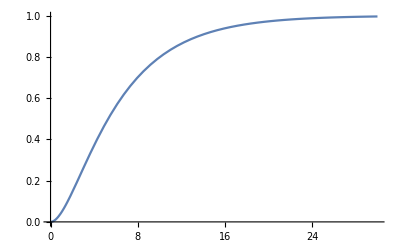

```mathematica
Plot[CDF[Y3,x],{x,0,30}]
```

### Obliczanie charakterystyk zmiennych losowych i prawdopodobieństw

Wartość oczekiwana wyrażenia zawierającego zmienną losową (należy podać rozkład zmiennej losowej w postaci x\[Distributed]Rozkład, symbol \[Distributed]  wprowadzamy wpisując   Esc dist Esc)

```mathematica
Expectation[x,x\[Distributed]X1]
```

0

```mathematica
Expectation[x^2 -x,x\[Distributed]BinomialDistribution[3,0.2]]
```

0.24

```mathematica
Expectation[x+2 y,{x\[Distributed]X2, y\[Distributed]X3}]
```

-1/12

Wariancja

```mathematica
Variance[X2]
```

```mathematica
Variance[PoissonDistribution[2]]
```

Odchylenie standardowe

```mathematica
StandardDeviation[X3]
```

Kwantyle
W celu wyznaczenia kwantyla rzędu q użyjemy funkcji Quantile[rozkład, q]

```mathematica
Quantile[X1,0.1]
```

-1.28155

```mathematica
Quantile[X2,{1/4,1/2,3/4}] (* kwartyle rozkładu X2 *)
```

{1/2 (2-√7),1/2 (2-√5),1/2 (2-√3)}

Prawdopodobieństwo

```mathematica
Probability[x<0, x\[Distributed]X1]
```

1/2

```mathematica
Probability[x==0,x\[Distributed]BernoulliDistribution[3/4]]
```

1/4

```mathematica
Probability[x≥y,{x\[Distributed]X2,y\[Distributed]X3}]
```

5/12

```mathematica
Probability[x^2 +y^2<1/4,{x\[Distributed]X3, y\[Distributed]X2}]
```

π/4

```mathematica
Probability[x<y\[Conditioned]y>0,{x\[Distributed]X3, y\[Distributed]X2}] (* prawdopodobieństwo warunkowe zdarzenia x<y, przy warunku y>0, \[Conditioned]- Esc cond Esc  *)
```

13/18

```mathematica
Probability[x<y,{x\[Distributed]X3, y\[Distributed]X2}]
```

5/12

### Dystrybuanty i gęstości

Dystrybuanta

```mathematica
CDF[ExponentialDistribution[2],x]
```

Piecewise[{{1-ⅇ^(-2 x), x≥0}, {0, True}}]

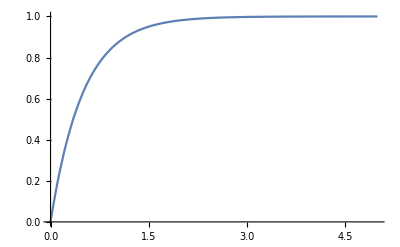

```mathematica
Plot[CDF[ExponentialDistribution[2],x],{x,0,5},PlotRange->All]
```

```mathematica
F[x_]:=CDF[PoissonDistribution[2],x]
```

```mathematica
F[x]
```

Piecewise[{{GammaRegularized[1+Floor[x],2], x≥0}, {0, True}}]

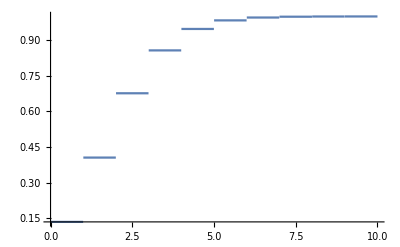

```mathematica
Plot[F[x],{x,0,10}]
```

Gęstość

```mathematica
f[x_]=PDF[ChiSquareDistribution[3],x]
```

Piecewise[{{(ⅇ^(-x/2) √x)/(√(2 π)), x>0}, {0, True}}]

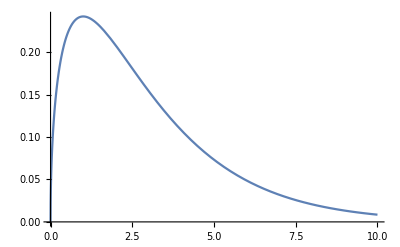

```mathematica
Plot[f[x],{x,0,10}]
```

```mathematica
f[n_]=PDF[GeometricDistribution[0.1],n]
```

Piecewise[{{0.1 0.9^n, n≥0}, {0, True}}]

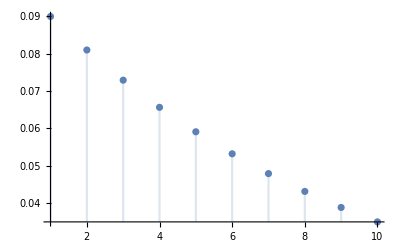

```mathematica
DiscretePlot[f[k],{k,Range[10]}]
```

Rozkład geometryczny jest rozkładem dyskretnym, więc nie posiada gęstości. W zamian wyznaczona została funkcja masy prawdopodobieństwa. f[k] to wartość prawdopodobieństwa tego, że zmienna losowa przyjmie wartość k.

```mathematica
sigma={{4,2},{2,3}}; (* Wykres funkcji gęstości prawdopodobieństwa dwuwymiarowego rozkładu normalnego z macierzą kowariancji sigma i wektorem średnich mu *)
mu={1,4};
Plot3D[PDF[MultinormalDistribution[mu,sigma],{x,y}],{x,-10,10},{y,-10,10}, PlotRange->All]
```

-Graphics3D-

```mathematica
sigma//MatrixForm
```

(4 | 2
2 | 3)

## 2. Generowanie wartości zmiennych losowych i symulacja procesów stochastycznych

### Liczby, wektory, macierze

```mathematica
RandomVariate[NormalDistribution[20,5]]
```

17.7903

```mathematica
RandomVariate[ExponentialDistribution[3],10]
```

{0.767453,0.402076,0.00340807,1.11083,0.217198,0.182482,0.143266,0.269998,0.77502,0.974509}

```mathematica
RandomVariate[PoissonDistribution[2],{3,4}]//MatrixForm
```

(3 | 1 | 0 | 2
1 | 1 | 2 | 1
6 | 1 | 4 | 3)

### Procesy losowe

```mathematica
RandomFunction[PoissonProcess[1],{0,5}]; (* symulacja procesu Poissona w przedziale czasu [0,5] *)
```

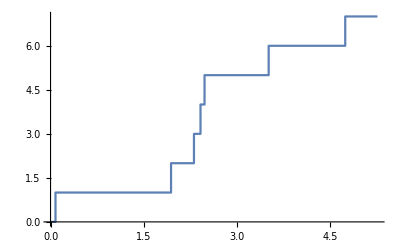

```mathematica
ListStepPlot[%] (* % przekazuje funkcji ostatni output, %k przekazuje output k-ty *)
```

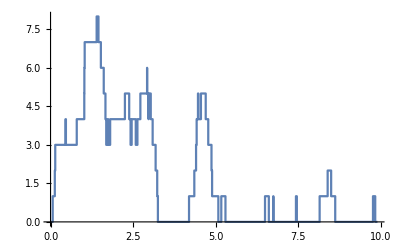

```mathematica
ListStepPlot[RandomFunction[QueueingProcess[3,4],{0,10}]] (* Symulacja modelu kolejkowego M/M/1 z parametrem strumienia wejściowego 3 i parametrem obsługi 4 *)
```

## 3. Statystyka

```mathematica
SeedRandom[3]
```

```mathematica
data1=RandomVariate[NormalDistribution[10,2],100];
data2=RandomVariate[ExponentialDistribution[0.4],100];
data3=RandomVariate[MultinormalDistribution[mu,sigma],1000];
```

### Statystyka opisowa

```mathematica
Mean[data1]
```

9.72077

```mathematica
Median[data1]
```

9.85953

```mathematica
Variance[data1]
```

4.00732

```mathematica
StandardDeviation[data1]
```

2.00183

```mathematica
Quantile[data1,0.2] (* kwantyl rzędu 0.2 *)
```

7.96707

### Wizualizacja

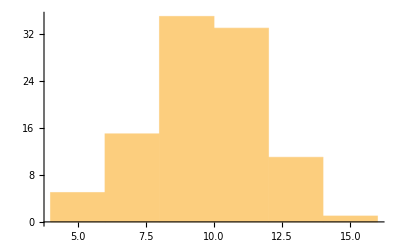

```mathematica
Histogram[data1]
```

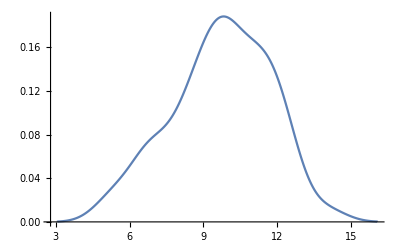

```mathematica
SmoothHistogram[data1] (* wykres estymowanej gęstości zmiennej data1 *)
```

```mathematica
Histogram3D[data3]
```

-Graphics3D-

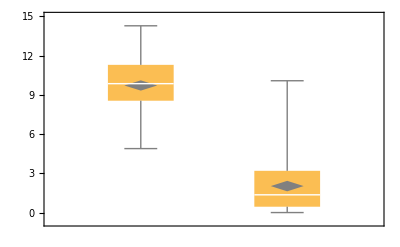

```mathematica
BoxWhiskerChart[{data1, data2}, "Diamond"]  (* opcja Diamond wyświetla przedział ufności dla wartości średniej *)
```

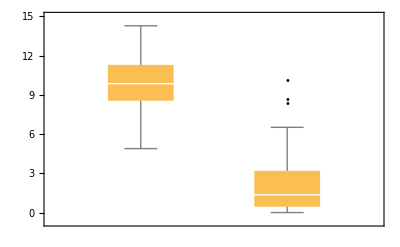

```mathematica
BoxWhiskerChart[{data1, data2},"Outliers"]  (* wyświetlenie wartości odstających, inne opcje opisane w dokumentacji *)
```

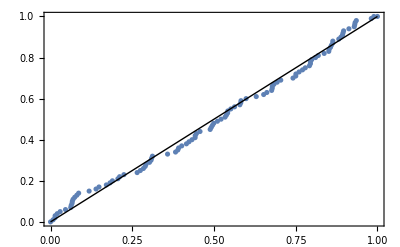

```mathematica
ProbabilityPlot[data1]  (* wykres prawdopodobieństwa rozkładu data1 względem rozkładu normalnego (wykres normalności) *)
```

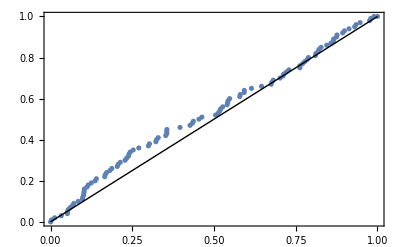

```mathematica
ProbabilityPlot[data2,ExponentialDistribution[0.45]] (* wykres rozkładu data2 względem wybranego rozkładu *)
```

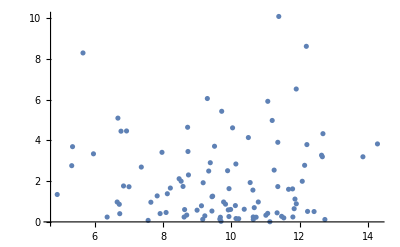

```mathematica
ListPlot[Table[{data1[[i]],data2[[i]]},{i,1,100}]] (* wykres rozrzutu data1 względem data2 (do elementów list odwołujemy się przez lista[[indeks]]), numerowanie od 1 *)
```

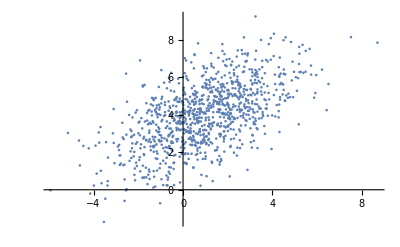

```mathematica
ListPlot[data3]
```

### Testowanie hipotez statystycznych

Dopasowanie rozkładu. Domyślnie dopasowywany jest rozkład normalny, w wyniku otrzymujemy wartość p dla testu weryfikującego H_0: rozkład data1 jest normalny

```mathematica
DistributionFitTest[data1]
```

0.314988

```mathematica
DistributionFitTest[data2]
```

0

Można dopasowywać inne rozkłady i wybrać test (domyślnie automatycznie jest wybierany najmocniejszy test, który do wprowadzonych danych może być zastosowany)

```mathematica
DistributionFitTest[data2,ExponentialDistribution[0.35]]
```

0.00314966

```mathematica
DistributionFitTest[data2,ExponentialDistribution[0.4],"TestData"]
```

{0.442833,0.0558217}

```mathematica
H=DistributionFitTest[data1,Automatic,"HypothesisTestData"]; (* wynik działania funkcji DistributionFitTest z argumentem "HypothesisTestData" jest obiektem, z którego możemy pobrać interesujące nas informacje *)
H["TestDataTable",All]  (* np. tablicę wyników wszystkich przeprowadzonych testów *)
```

| Statistic | P-Value
Anderson-Darling | 0.487908 | 0.225164
Baringhaus-Henze | 0.466025 | 0.212737
Cramér-von Mises | 0.066658 | 0.314988
Jarque-Bera ALM | 2.1038 | 0.284486
Kolmogorov-Smirnov | 0.0539852 | 0.678045
Kuiper | 0.0963122 | 0.479378
Mardia Combined | 2.1038 | 0.284486
Mardia Kurtosis | -0.798496 | 0.424583
Mardia Skewness | 1.48042 | 0.223709
Pearson χ^2 | 9.72 | 0.465393
Shapiro-Wilk | 0.983765 | 0.257861
Watson U^2 | 0.0568635 | 0.377305

```mathematica
H2 = DistributionFitTest[data2, ExponentialDistribution[0.4], "HypothesisTestData"];
H2["TestDataTable", All]
```

| Statistic | P-Value
Anderson-Darling | 2.50957 | 0.0490947
Cramér-von Mises | 0.442833 | 0.0558217
Kolmogorov-Smirnov | 0.126378 | 0.0750181
Kuiper | 0.132225 | 0.216181
Pearson χ^2 | 16.74 | 0.159642
Watson U^2 | 0.0948935 | 0.307364

```mathematica
H["Properties"]
```

{AllTests,AndersonDarling,AutomaticTest,BaringhausHenze,CramerVonMises,DegreesOfFreedom,DistanceToBoundary,FittedDistribution,FittedDistributionParameters,HypothesisTestData,JarqueBeraALM,KolmogorovSmirnov,Kuiper,MardiaCombined,MardiaKurtosis,MardiaSkewness,PearsonChiSquare,Properties,PValue,PValueTable,ShapiroWilk,ShortTestConclusion,SzekelyEnergy,TestConclusion,TestData,TestDataTable,TestEntries,TestStatistic,TestStatisticTable,WatsonUSquare}

```mathematica
H["TestConclusion"]
```

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is not rejected at the 5 percent level based on the Cramér-von Mises test.

```mathematica
DistributionFitTest[data2, ExponentialDistribution[0.4], "TestConclusion", SignificanceLevel->0.01]
```

The null hypothesis that the data is distributed according to the ExponentialDistribution[0.4] is not rejected at the 1. percent level based on the Cramér-von Mises test.